```mathematica
(* 01 *)
DSolveValue[y'[x]==x^3 Cos[x],y[x],x]
```

C[1]+3 (-2+x^2) Cos[x]+x (-6+x^2) Sin[x]

```mathematica
(* 02 *)
DSolveValue[{y'[x]==x^3 Cos[x],y[3]==6},y[x],x]
```

6-21 Cos[3]-6 Cos[x]+3 x^2 Cos[x]-9 Sin[3]-6 x Sin[x]+x^3 Sin[x]

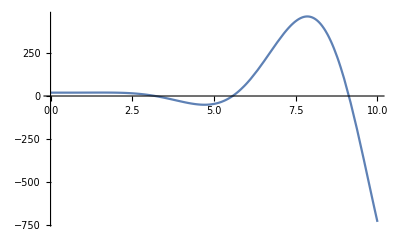

```mathematica
(* 03 *)
f = DSolveValue[{y'[x]==x^3 Cos[x],y[3]==6},y[x],x];
Plot[f,{x,0,10}]
```

```mathematica
(* 04 *)
DSolveValue[y''[x]+y'[x]==x^2 √x,y[x],x]
```

(2 x^(7/2))/7-ⅇ^-x C[1]+C[2]+(ⅇ^-x √-x Gamma[7/2,-x])/(√x)

```mathematica
(* 05 06 07 08 无法解答*)
(* 09 *)
```

```mathematica
NDSolve[{y'[x]==x^3 Cos[x],y[3]==6},y[x],{x,0,5}]
```

{{y[x]→InterpolatingFunction[…][x]}}

```mathematica
(* 10 *)
NDSolveValue[{y'[x]==x^3 Cos[x],y[3]==6},y[x],{x,0,5}]
```

InterpolatingFunction[…][x]

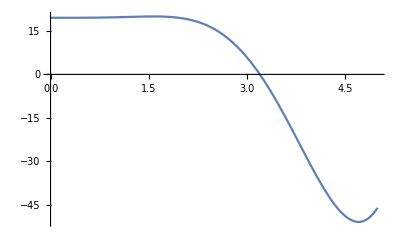

```mathematica
Plot[%20,{x,0.,5.}]
```